Variance of Z(t) function

```mathematica
VZT = ((Vzp + Vzq)/2+ 1/2((Ezp-Ezq)/2)^2) + ((Vzp - Vzq)/2)Sin[w t] + (1/2)*((Ezp-Ezq)/2)^2*Sin[2*w*t + Pi/2];
```

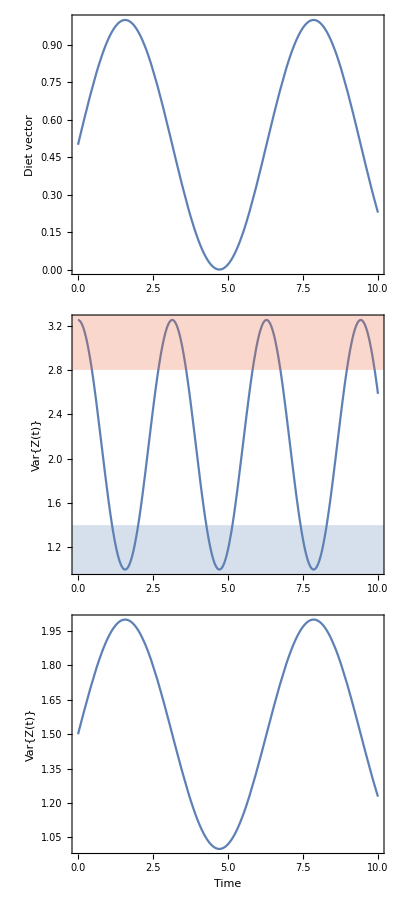

```mathematica
VarZtPlot = Column[{
Plot[1/2 + (1/2)*Sin[w t]/.{w->1},{t,0,10},AspectRatio->0.35,ImageSize->300,Frame->True,FrameLabel->{"","Diet vector",""}],
Show[{
Plot[VZT/.{w->1,Ezp->-15,Ezq->-12,Vzp->1,Vzq->1},{t,0,10},AspectRatio->0.35,Frame->True,ImageSize->300,FrameLabel->{"","Var{Z(t)}",Rotate["Different means",0Degree]}],
Graphics[{ColorData[97,1],Opacity[0.25],Rectangle[{-1,-1},{11,1.4}]}],
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{-1,2.8},{11,4}]}]
}],
Plot[VZT/.{w->1,Ezp->-15,Ezq->-15,Vzp->2,Vzq->1},{t,0,10},AspectRatio->0.35,Frame->True,ImageSize->300,FrameLabel->{"Time","Var{Z(t)}",Rotate["Different variances",0Degree]}]
},Spacings->0]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varZt.pdf",VarZtPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varZt.pdf

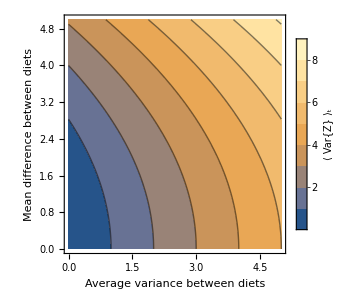

```mathematica
VarZContourPlot=ContourPlot[
 (AvgV+ 1/2(DiffE/2)^2) ,{AvgV,0,5},{DiffE,0,5},FrameLabel->{Style["Average variance between diets",FontSize->14],Style["Mean difference between diets",FontSize->14]},PlotLegends->BarLegend[Automatic,LegendLabel->"⟨ Var{Z} ⟩_t",LegendMarkerSize->200],ImageSize->300]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varzContour.pdf",VarZContourPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_varzContour.pdf

General E[X] and V[X]

```mathematica
EX =  X0 Exp[-λ t]+λ Exp[-λ t] Integrate[Exp[λ s] EZ[s],{s,0,t}]
VX = Exp[-2 λ t] λ^2  Integrate[Exp[2 λ s] V[s],{s,0,t}]
```

ⅇ^(-t λ) X0+ⅇ^(-t λ) λ ∫_0^t ⅇ^(s λ) EZ[s]ⅆs

ⅇ^(-2 t λ) λ^2 ∫_0^t ⅇ^(2 s λ) V[s]ⅆs

Sinusoidal input

```mathematica
EXsin= EX/.{EZ[s]-> αE+βE Sin[ω s]}
VXsin = VX/.{V[s]->VZT/.{t->s}}
```

ⅇ^(-t λ) X0+ⅇ^(-t λ) λ (((-1+ⅇ^(t λ)) αE)/λ+(βE (ω+ⅇ^(t λ) (-ω Cos[t ω]+λ Sin[t ω])))/(λ^2+ω^2))

1/16 ⅇ^(-2 t λ) λ^2 (-(Ezp^2-2 Ezp Ezq+Ezq^2+4 (Vzp+Vzq))/λ-((Ezp-Ezq)^2 λ)/(w^2+λ^2)+(8 (Vzp-Vzq) w)/(w^2+4 λ^2)+ⅇ^(2 t λ) ((Ezp^2-2 Ezp Ezq+Ezq^2+4 (Vzp+Vzq))/λ-(8 (Vzp-Vzq) w Cos[t w])/(w^2+4 λ^2)+((Ezp-Ezq)^2 λ Cos[2 t w])/(w^2+λ^2)+(16 (Vzp-Vzq) λ Sin[t w])/(w^2+4 λ^2)+((Ezp-Ezq)^2 w Sin[2 t w])/(w^2+λ^2)))

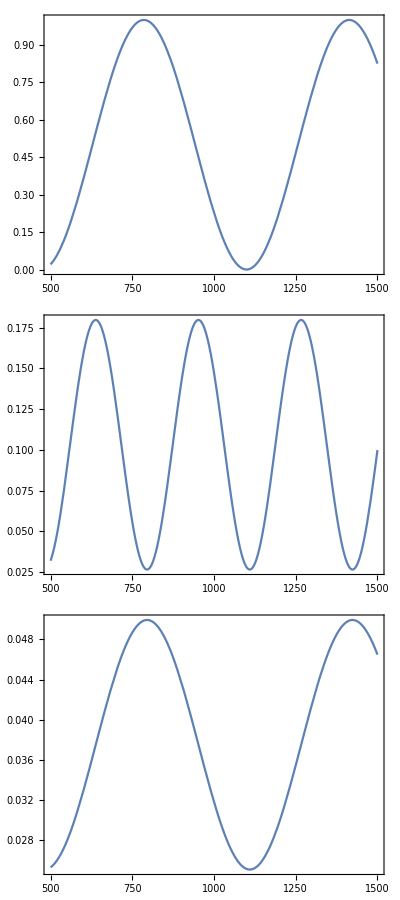

```mathematica
Column[{
Plot[1/2 + (1/2)*Sin[w t]/.{w->0.01},{t,500,1500},AspectRatio->0.35,Frame->True,ImageSize->300],
Plot[VXsin /.{λ->0.05,w->0.01,Ezp->-15,Ezq->-10,Vzp->1,Vzq->1},{t,500,1500},AspectRatio->0.35,Frame->True,ImageSize->300],
Plot[VXsin /.{λ->0.05,w->0.01,Ezp->-15,Ezq->-15,Vzp->2,Vzq->1},{t,500,1500},AspectRatio->0.35,Frame->True,ImageSize->300]
}]
```